#### 反复迭代近似

```mathematica
c=3 10^8; (*m/s*)
pi=3.14159;
λ=1550 10^-9; (*m*)
loss = (2 pi c 0.02 10^-9)/λ^2/2; (*2/τ*)
ω0=2 pi c/λ;
κ=1.86 10^-4; (*K^-1*)
τ0=1 10^-6; (*s*)
β=8 10^-12; (*m/W*)
ρ=2.3 10^3; (*kg/m^3*)
heatCapacity=705;(*J/kg/K*)
neff=2.35;
λfsr=6.4 10^-9;
L=λ^2/(neff λfsr);
Vgeo=pi L (220 10^-9 450 10^-9);
V=8.24 Vgeo;
coef = (ω0 κ τ0 β c^2)/(ρ heatCapacity Vgeo^2)
```

4.06909×10^37

```mathematica
p
```

```mathematica
1/loss
```

1.27457×10^-10

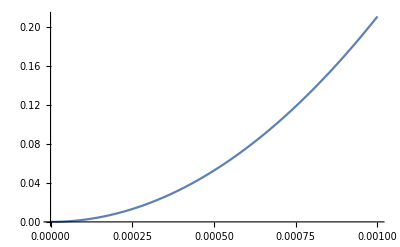

```mathematica
Plot[coef (Pin (loss/2)/(loss)^2)^2 λ^2/(2 pi c) 10^9,{Pin,0,10^-3}]
```

|a|^2=P_in  (1/τ_1)/(1/τ_1+1/τ_in)^2 
1 mW -->  0.03 nm
Algorithm:
fix Pin , e.g. Pin=1*10^-3 mW
do while:
	|a|^2=P_in  (1/τ_1)/((1/τ_1+1/τ_in)^2+Δ ω_shift^2) 
	Δ ω_shift = coef |a|^4
untill Δ ω_shift converge

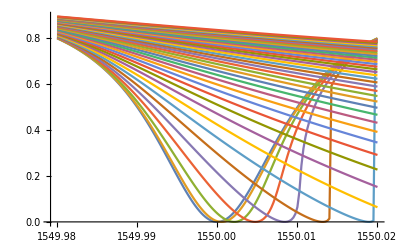

```mathematica
(*透射谱，更宽范围，备份*)
power=Range[0,20 10^-4,5 10^-5];
wave=Range[1550-0.02,1550+0.02,0.00025];
Ans1 = Table[0,Length@power,Length@wave];
For[k=1,k<=Length@power,k++,
	Pin=power[[k]];
	predw=0;
	pretot=0;
	For[j=1,j<=Length@wave,j++,
		repeat = 1000;
		eta = Subdivide[0.5,0.9,repeat]; 
		ans = Table[0,repeat];
		dw0=2 pi c/(wave[[j]]* 10^-9)-ω0;
		dw=predw;
		tot=pretot;
		For[i=1,i<=repeat,i++,
			a = Pin (loss/2)/((loss)^2+(dw0+dw)^2);
			tot=tot*eta[[i]]+coef a^2*(1-eta[[i]]);
			dw=tot;
			ans[[i]]=dw;
		];
		predw=dw;
		pretot=tot;
		dw=ans[[-1]]+dw0;
		Ans1[[k,j]]=Abs[dw/(loss + ⅈ dw)]^2;
	]
];

ListLinePlot[Table[Transpose@{wave,Ans1[[k,;;]]},{k,1,Length@power}]]
(*ListLinePlot[ans,PlotRange->All]*)
```

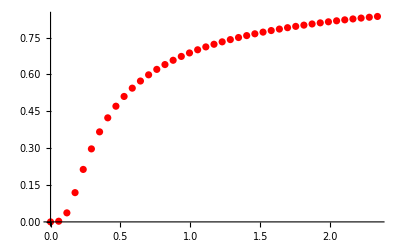

```mathematica
newPower=power*10^3/0.7274179570231867*0.85;
newWave=wave+0.45;
T=Ans1[[;;,81]];
data = Transpose@{newPower,T};
ListPlot[data, PlotStyle -> Red]
```

```mathematica
power=Range[0,4 10^-4,1 10^-5];
wave=Range[1550-0.05,1550+0.05,0.00025];
```

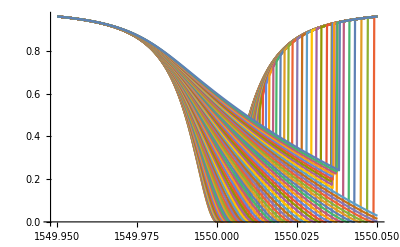

```mathematica
(*透射谱，更宽范围，备份*)
power=Range[0,6 10^-4,1 10^-5];
wave=Range[1550-0.05,1550+0.05,0.00025];
Ans = Table[0,Length@power,Length@wave];
For[k=1,k<=Length@power,k++,
	Pin=power[[k]];
	predw=0;
	pretot=0;
	For[j=1,j<=Length@wave,j++,
		repeat = 1000;
		eta = Subdivide[0.5,0.9,repeat]; 
		ans = Table[0,repeat];
		dw0=2 pi c/(wave[[j]]* 10^-9)-ω0;
		dw=predw;
		tot=pretot;
		For[i=1,i<=repeat,i++,
			a = Pin (loss/2)/((loss)^2+(dw0+dw)^2);
			tot=tot*eta[[i]]+coef a^2*(1-eta[[i]]);
			dw=tot;
			ans[[i]]=dw;
		];
		predw=dw;
		pretot=tot;
		dw=ans[[-1]]+dw0;
		Ans[[k,j]]=Abs[dw/(loss + ⅈ dw)]^2;
	]
];

ListLinePlot[Table[Transpose@{wave,Ans[[k,;;]]},{k,1,Length@power}]]
(*ListLinePlot[ans,PlotRange->All]*)
```

```mathematica
wave[[205]]-1550
```

0.001

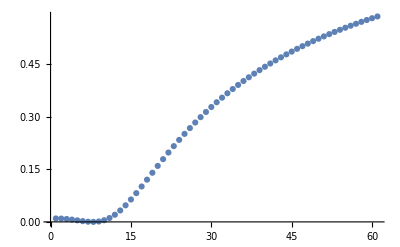

```mathematica
ListPlot@Ans[[;;,205]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\zxc27\Desktop\硅非线性激活函数

```mathematica
epe = Import["非线性数据\\actiExpMean_1.txt","Table"];
epe=epe[[1]]
```

{0.0110619,0.0184476,0.0804901,0.162327,0.23665,0.303286,0.371585,0.476373,0.555751}

```mathematica
Range[0.2,1,0.1]/2
```

9

```mathematica
1/0.7274179570231867*0.95
```

1.30599

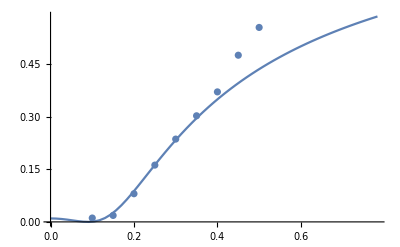

```mathematica
newPower=power*10^3*1.30598920583111;
T=Ans[[;;,205]];
data1 = Transpose@{newPower,T};
data2 = Transpose@{Range[0.2,1,0.1]/2,epe};
Show[ListLinePlot[data1],ListPlot[data2]]
```

```mathematica
Export["E:\\硅非线性激活函数\\非线性数据\\numericalTransmissionTickwave.txt",wave+0.45,"Table"]
```

E:\硅非线性激活函数\非线性数据\numericalTransmissionTickwave.txt

```mathematica
Export["非线性数据\\numericalTransmissionTickpower.txt",newPower,"Table"]
Export["非线性数据\\numericalTransmissionTickpower.txt",newPower,"Table"]
```

E:\硅非线性激活函数\非线性数据\numericalTransmissionTickpower.txt

```mathematica
Export["E:\\硅非线性激活函数\\非线性数据\\numericalTransmission.txt",Ans,"Table"]
```

E:\硅非线性激活函数\非线性数据\numericalTransmission.txt

```mathematica
Length@Ans[[1,;;]]
```

401

```mathematica
wave[[200]]
```

1550.

```mathematica
newPower=power*10^3/0.7274179570231867*0.85
```

{0.,0.0116852,0.0233703,0.0350555,0.0467407,0.0584258,0.070111,0.0817962,0.0934813,0.105166,0.116852,0.128537,0.140222,0.151907,0.163592,0.175277,0.186963,0.198648,0.210333,0.222018,0.233703,0.245388,0.257074,0.268759,0.280444,0.292129,0.303814,0.315499,0.327185,0.33887,0.350555,0.36224,0.373925,0.38561,0.397296,0.408981,0.420666,0.432351,0.444036,0.455721,0.467407}

{c1→0.545042,c2→0.241564,c3→11.744,c4→-0.046238}

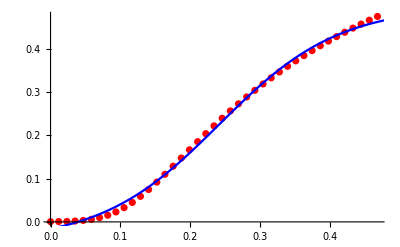

```mathematica
newPower=power*10^3*1.30598920583111;
T=Ans[[;;,205]];
data = Transpose@{newPower,T};

(* 定义 Sigmoid 模型 *)
model = c1  /(1+Exp[-((x - c2)^1)*c3])+c4 ;

(* 使用 NonlinearModelFit 拟合数据 *)
fit = NonlinearModelFit[data, model, {{c1,0.6},{c2,0.25},{c3,10},{c4,0}}, x, MaxIterations -> 1000];

(* 查看拟合结果 *)
fit["BestFitParameters"]

(* 绘制拟合曲线 *)
Show[
 ListPlot[data, PlotStyle -> Red],
 Plot[fit[x], {x, 0, 0.5}, PlotStyle -> Blue]
]

(*Export["E:\\硅非线性激活函数\\非线性数据\\actiNum.txt",T,"Table"];
Export["E:\\硅非线性激活函数\\非线性数据\\actiNumpower.txt",newPower,"Table"];
Export["E:\\硅非线性激活函数\\非线性数据\\actiNumwave.txt",newWave,"Table"];*)

(*ListPlot@Transpose@{newPower,T}*)
```

```mathematica
(*将工作目录设置为笔记本文件所在的目录*)
SetDirectory[NotebookDirectory[]];
```

```mathematica
FileNames["*","C:\\Users\\zxc27\\Documents"]
```

{C:\Users\zxc27\Documents\desktop.ini,C:\Users\zxc27\Documents\LabVIEW Data,C:\Users\zxc27\Documents\My Music,C:\Users\zxc27\Documents\My Pictures,C:\Users\zxc27\Documents\My Videos,C:\Users\zxc27\Documents\自定义 Office 模板,C:\Users\zxc27\Documents\Thorlabs,C:\Users\zxc27\Documents\WeChat Files,C:\Users\zxc27\Documents\Wolfram Mathematica}

```mathematica
X = Range[0.1,0.5,0.05];
ExpAct=Import["非线性数据\\actiExpMean_1.txt","Table"];
Y=ExpAct[[1]];
```

```mathematica
X
```

{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5}

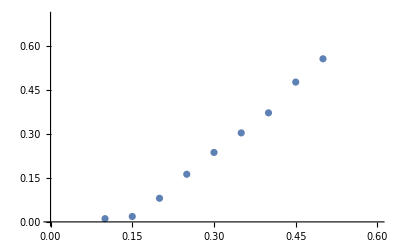

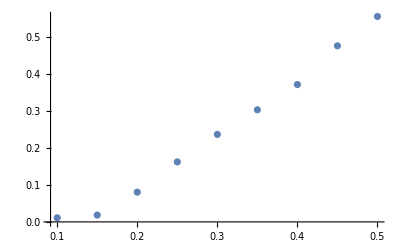

```mathematica
ListPlot[data,PlotRange->{{0,0.6},{0,0.7}}]
```

{alpha→53.4409,beta→-0.174322,c1→0.03962,c2→1.55547}

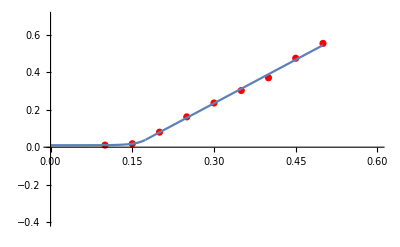

```mathematica
(* 定义 CELU 函数 *)
celu[x_, alpha_,beta_,c1_,c2_] := c1+c2*Piecewise[{{x+beta, x+beta > 0}, {1/alpha (Exp[alpha (x+beta)] - 1), x+beta <= 0}}];

(* 准备数据 *)
data = Transpose@{X,Y};
weights = {10,10,5,1,1,1,1,1,1};

(* 使用 NonlinearModelFit 拟合 *)
fit = NonlinearModelFit[data, celu[x, alpha,beta,c1,c2], {alpha,beta,c1,c2}, x, Weights -> weights];

(* 查看拟合结果 *)
fit["BestFitParameters"]

(* 绘制拟合曲线 *)
Show[
 ListPlot[data, PlotStyle -> Red, PlotRange->{{0,0.6},{-0.4,0.7}}],
 Plot[fit[x], {x, 0, 0.5}, PlotRange -> All]
]
```

```mathematica
fit
```

FittedModel[0.0549704+1.51853 ({ | «1»)]

```mathematica
beta
```

beta

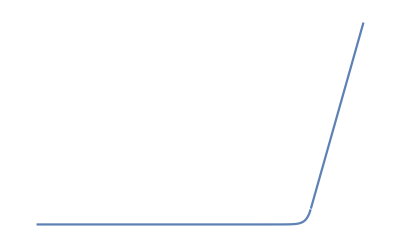

```mathematica
Plot[fit[x], {x,-1, 0.4},PlotRange->All,Axes->False]
```

```mathematica
X = Table[x,{x,0,0.53,0.005}];
Y = Table[fit[x],{x,0,0.53,0.005}];
Export["非线性数据\\CeLUpower.txt",X,"Table"]
Export["非线性数据\\CeLU.txt",Y,"Table"]
```

非线性数据\CeLUpower.txt

非线性数据\CeLU.txt

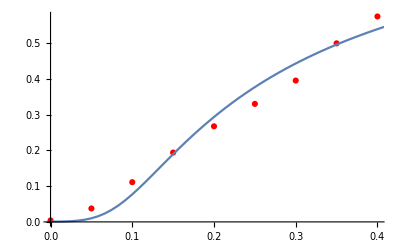

```mathematica
newPower=power*10^3/0.7274179570231867*0.6;
newWave=wave+0.45;
T=Ans[[;;,200]];
data1 = Transpose@{newPower,T};
Show[ListPlot[data, PlotStyle -> Red, PlotMarkers -> Automatic],ListLinePlot[data1]]
```

```mathematica
Export["非线性数据\\actiNum.txt",T,"Table"];
Export["非线性数据\\actiNumpower.txt",newPower,"Table"];
```

```mathematica
X = Table[x,{x,0,0.5,0.005}];
Y = Table[fit[x],{x,0,0.5,0.005}];
Export["E:\\硅非线性激活函数\\非线性数据\\sigmoidX.txt",X,"Table"]
Export["E:\\硅非线性激活函数\\非线性数据\\sigmoid.txt",Y,"Table"]
```

E:\硅非线性激活函数\非线性数据\sigmoidX.txt

E:\硅非线性激活函数\非线性数据\sigmoid.txt

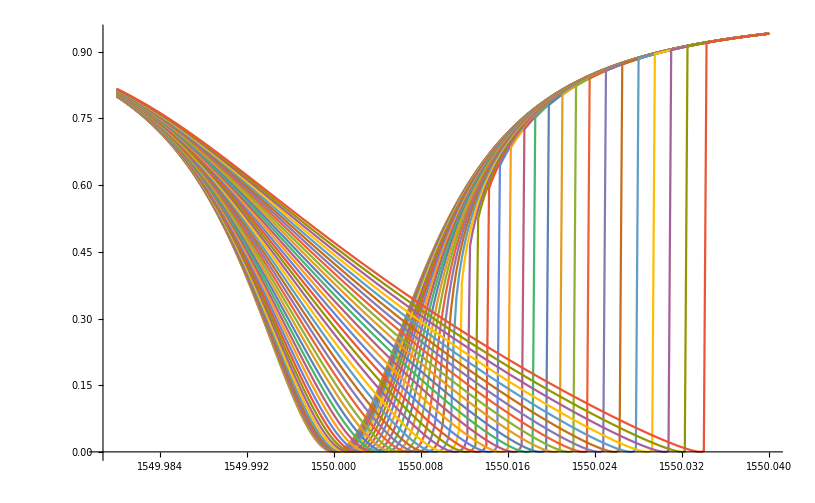

```mathematica
(*使用比例求和，提高最新值的权重，求全部透射谱*)
power=Range[0,4 10^-4,1 10^-5];
wave=Range[1550-0.02,1550+0.04,0.00025];
Ans = Table[0,Length@power,Length@wave];
For[k=1,k<=Length@power,k++,
	Pin=power[[k]];
	predw=0;
	pretot=0;
	For[j=1,j<=Length@wave,j++,
		repeat = 1000;
		eta = Subdivide[0.5,0.9,repeat]; 
		ans = Table[0,repeat];
		dw0=2 pi c/(wave[[j]]* 10^-9)-ω0;
		dw=predw;
		tot=pretot;
		For[i=1,i<=repeat,i++,
			a = Pin (loss/2)/((loss)^2+(dw0+dw)^2);
			tot=tot*eta[[i]]+coef a^2*(1-eta[[i]]);
			dw=tot;
			ans[[i]]=dw;
		];
		predw=dw;
		pretot=tot;
		dw=ans[[-1]]+dw0;
		Ans[[k,j]]=Abs[dw/(loss + ⅈ dw)]^2;
	]
];

ListLinePlot[Table[Transpose@{wave,Ans[[k,;;]]},{k,1,Length@power}]]
(*ListLinePlot[ans,PlotRange->All]*)
```

```mathematica
experiment = Import["E:\\硅非线性激活函数\\非线性数据\\dataPeakShift.txt","Table"];
experiment = Transpose@experiment
```

{{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},{0.01,0.0225,0.04,0.0625,0.09,0.1225,0.16,0.2025,0.25},{1550.45,1550.45,1550.46,1550.46,1550.46,1550.46,1550.47,1550.47,1550.48},{0.000507826,0.00058326,0.000355247,0.000343467,0.000377705,0.000727662,0.000343467,0.000377705,0.000388448}}

```mathematica
N@power
experiment[[1,;;]]
```

{0.,0.00005,0.0001,0.00015,0.0002,0.00025,0.0003,0.00035,0.0004,0.00045,0.0005,0.00055,0.0006,0.00065,0.0007,0.00075,0.0008}

{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5}

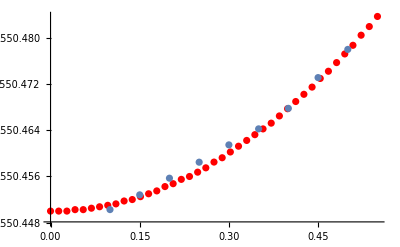

```mathematica
ResoWave = Table[0,Length@power];
For[i=1,i<=Length@power,i++,
	arr = Ans[[i,;;]];
	minValue=Min[arr];
	minPosition=Position[arr,minValue];
	ResoWave[[i]]=wave[[minPosition[[1,1]]]];
]
Show[ListPlot[Transpose@{(power*10^3/0.7274179570231867),ResoWave+0.45},PlotStyle->Red],
ListPlot@Transpose@{experiment[[1,;;]],experiment[[3,;;]]}]
```

```mathematica
Export["E:\\硅非线性激活函数\\非线性数据\\numerical.txt",Transpose@{(power*10^3/0.7274179570231867),ResoWave+0.45},"Table"]
```

E:\硅非线性激活函数\非线性数据\numerical.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["numerical.txt"]]]
```

```mathematica
SystemOpen["numerical.txt"]
```

```mathematica
√(0.11094729548595877/0.20967598139325386)
(1550.4506099551484-1549.9999498039217)
```

0.727418

0.45066

```mathematica
Transpose@{power*10^3,ResoWave}
Transpose@{experiment[[1,;;]],experiment[[3,;;]]}
```

{{0,1550.},{1/20,1550.},{1/10,1550.},{3/20,1550.},{1/5,1550.},{1/4,1550.},{3/10,1550.01},{7/20,1550.01},{2/5,1550.01},{9/20,1550.01},{1/2,1550.01},{11/20,1550.02},{3/5,1550.02},{13/20,1550.02},{7/10,1550.03},{3/4,1550.03},{4/5,1550.03}}

{{0.1,1550.45},{0.15,1550.45},{0.2,1550.46},{0.25,1550.46},{0.3,1550.46},{0.35,1550.46},{0.4,1550.47},{0.45,1550.47},{0.5,1550.48}}

FittedModel[1550.45+0.110947 x^2]

1550.45+0.110947 x^2

FittedModel[1550.+0.209676 x^2]

1550.+0.209676 x^2

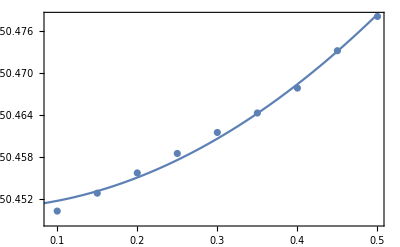

```mathematica
datatofit1 =  Transpose@{experiment[[1,;;]],experiment[[3,;;]]};
nlm1=NonlinearModelFit[datatofit1,(c1*x)^2 + c2,{c1,c2},x]
Normal[nlm1]

datatofit2 =  Transpose@{power*10^3,ResoWave};
nlm2=NonlinearModelFit[datatofit2,(c1*x)^2 + c2,{c1,c2},x]
Normal[nlm2]

Show[ListPlot[datatofit1],Plot[nlm1[x],{x,0,0.5}],ListPlot[datatofit2],Plot[nlm2[x],{x,0,0.8}],Frame->True]
```

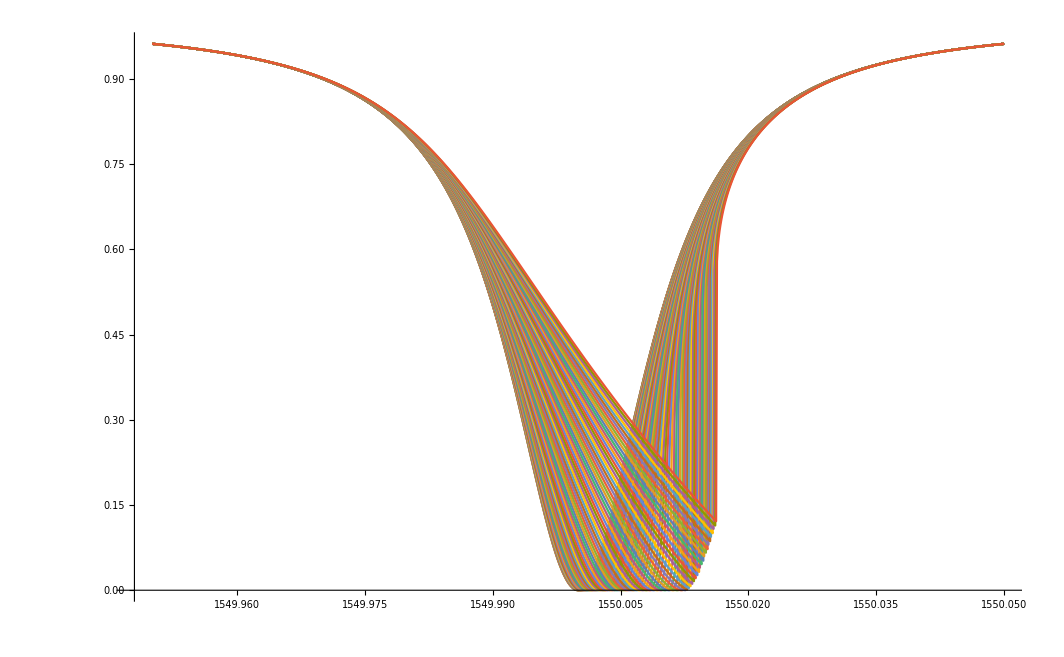

```mathematica
未使用渐变eta，同时未采用近邻参数迁移初始化
```

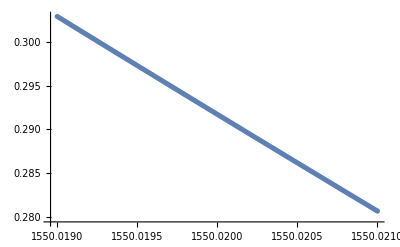

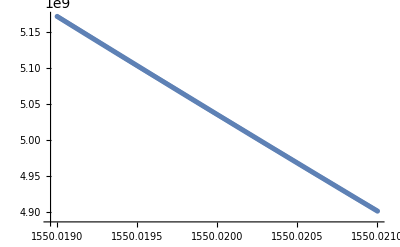

```mathematica
(*部分透射谱观察*)
power=Range[10 10^-4,10 10^-4,10^-4];
wave=Range[1550.02-0.001,1550.02+0.001,0.00001];
Ans = Table[0,Length@power,Length@wave];
dwlist=Table[0,Length@wave];
For[k=1,k<=Length@power,k++,
	Pin=power[[k]];
	predw=0;
	pretot=0;
	For[j=1,j<=Length@wave,j++,
		repeat = 1000;
		eta = Subdivide[0.5,0.9,repeat]; 
		ans = Table[0,repeat];
		dw0=2 pi c/(wave[[j]]* 10^-9)-ω0;
		dw=predw;
		tot=pretot;
		For[i=1,i<=repeat,i++,
			a = Pin (loss/2)/((loss)^2+(dw0+dw)^2);
			tot=tot*eta[[i]]+coef a^2*(1-eta[[i]]);
			dw=tot;
			ans[[i]]=dw;
		];
		predw=dw;
		pretot=tot;
		dw=ans[[-1]]+dw0;
		dwlist[[j]]=dw;
		Ans[[k,j]]=Abs[dw/(loss + ⅈ dw)]^2;
	]
];

ListPlot[Table[Transpose@{wave,Ans[[k,;;]]},{k,1,Length@power}]]
ListPlot[Transpose@{wave,dwlist}]
(*ListLinePlot[ans,PlotRange->All]*)
```

-1.55345×10^10

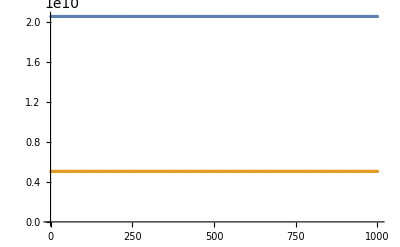

```mathematica
(*判断突变点数值特征*)
repeat = 1000;
ans1 = Table[0,repeat];
ans2 = Table[0,repeat];
Pin=10 10^-4;
pt = 1550.0198;
	eta = Subdivide[0.5,0.9,repeat]; 
	dw0=2 pi c/((pt)* 10^-9)-ω0
	dw=2.059665619199878*^10;
	tot=2.059665619199878*^10;
	For[i=1,i<=repeat,i++,
		a = Pin (loss/2)/((loss)^2+(dw0+dw)^2);
		(*tot = coef a^2;*)
		tot=tot*eta[[i]]+coef a^2*(1-eta[[i]]);
		dw=tot;
		ans2[[i]]=dw;
	];
ListPlot[{ans2,ans2+dw0},PlotRange->All]
```

```mathematica
ans2[[-1]]
```

2.05967×10^10

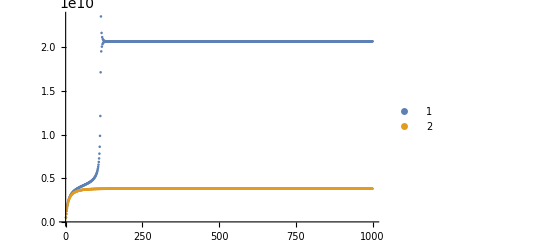

```mathematica
ListPlot[{ans1,ans2},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
For[i=1,i<Length@dwlist,i++,
If[dwlist[[i]]*dwlist[[i+1]]<0,Print[NumberForm[wave[[i]],20]];Break[];];
]
```

1550.0199

```mathematica
wave[[2]]-wave[[1]]
```

0.0001

```mathematica
wave[[i+2]]
```

1550.02

```mathematica
ListLinePlot[Table[Transpose@{wave,Ans[[k,;;]]},{k,1,Length@power}],PlotLegends->Automatic]
```

0.0226539

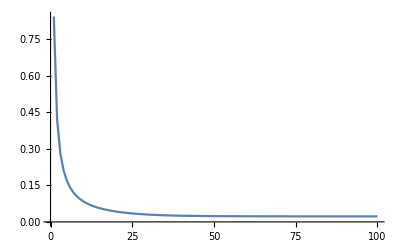

```mathematica
(*求和平均迭代法*)
repeat = 100;
ans = Table[0,repeat];
Pin=40 10^-4;
dw=0;
tot=0;
For[i=1,i<=repeat,i++,
	a = Pin (loss/2)/((loss)^2+dw^2);
	tot=tot+coef a^2;
	dw=tot/i;
	ans[[i]]=dw λ^2/(2 pi c) 10^9;
]
ans[[-1]]
ListLinePlot[ans,PlotRange->All]
```

0.0225968

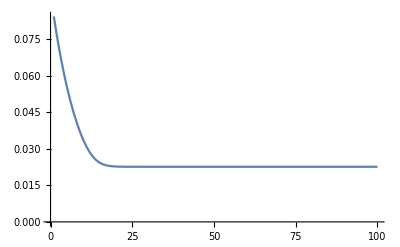

```mathematica
(*比例优化迭代法*)
repeat = 100;
ans = Table[0,repeat];
Pin=40 10^-4;
dw=0;
tot=0;
For[i=1,i<=repeat,i++,
	a = Pin (loss/2)/((loss)^2+dw^2);
	eta=0.9;
	tot=tot*eta+coef a^2*(1-eta);
	dw=tot;
	ans[[i]]=dw λ^2/(2 pi c) 10^9;
]
ans[[-1]]
ListLinePlot[ans,PlotRange->All]
```

```mathematica
Solve[(ⅈ (ω0-ω-coef Abs[a]^4)+2/τ)a==√(2/τ) s, a]
```

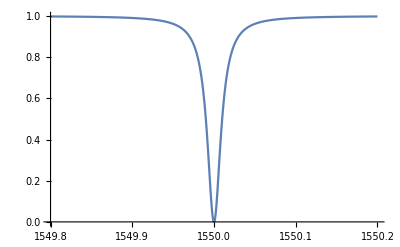

```mathematica
ω0=2 pi c/λ;
Plot[Abs[(2 pi c/(lambda* 10^-9)-ω0)/(loss + ⅈ(2 pi c/(lambda *10^-9)-ω0))]^2,{lambda,(1550-0.2),(1550+0.2)},PlotRange->All]
```